```mathematica
Remove["Global`*"]
```

```mathematica
SetDirectory["L:\\local-expdata\\FO-C5\\3rd-Run\\2011_04_22\\"];
fileList=StringDrop[#,StringLength["  path: "]]&/@(ReadList["Spectroscopy Survey - qubit1-7.par",String]//Select[#,StringMatchQ[#,___~~"path:"~~___]&]&);
ext=".txt";
fluxList=Import["Spectroscopy Survey - qubit1-7.txt","Table"]//Flatten//Rest;Length[fluxList]
```

121

```mathematica
header=Import[fileList[[1]]<>ext,"Table"][[1]]
```

{f,px1,p10,p11,p01,p00,p1x,p1x_fit}

```mathematica
pos=Position[header,#]&/@{"f","px1","p1x"}//Flatten;
data=(Import[#<>".txt","Table"]//Rest//Transpose//#[[pos]]&//Transpose//Sort)&/@fileList;
freqList=(data[[1]]//Transpose)[[1]];
{Length[data],Length[freqList]}
```

{121,601}

```mathematica
dataRange1={rangeFlux,rangeFreq}={{fluxList[[1]],fluxList[[-1]]},{freqList[[1]],freqList[[-1]]}}
```

{{1.26,1.32},{5.05,5.17}}

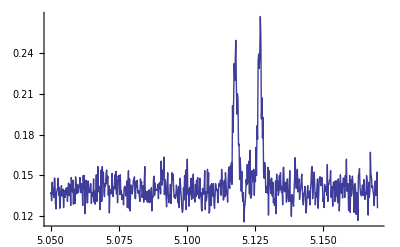

```mathematica
Most/@(data[[35]])//ListPlot[#,Joined->True,PlotRange->All]&
```

```mathematica
addX[x_,listYZ_]:=Prepend[#,x]&/@listYZ
```

```mathematica
datap1x=Sort/@Map[Drop[#,{2}]&/@#&,data];
datapx1=Sort/@Map[Most/@#&,data];
datap1xx1=Sort/@Map[{#[[1]],#[[2]]+#[[3]]}&/@#&,data];
```

```mathematica
datap1xF=MapThread[addX[#1,#2]&,{fluxList,datap1x}];
datapx1F=MapThread[addX[#1,#2]&,{fluxList,datapx1}];
datap1xx1F=MapThread[addX[#1,#2]&,{fluxList,datap1xx1}];
```

```mathematica
dataRange1
```

{{1.26,1.32},{5.05,5.17}}

```mathematica
datap1xZ=Map[#[[3]]&,datap1xF,{2}];
{min1x,max1x}=datap1xZ//Flatten//{Min[#],Max[#]}&
datap1xZNorm=(datap1xZ-min1x)/(max1x-min1x);
ArrayPlot[Transpose[datap1xZNorm],DataReversed->True,AspectRatio->1,FrameTicks->{{{{0,rangeFreq[[1]]},{601,rangeFreq[[2]]}},None},{{{0,rangeFlux[[1]]},{121,rangeFlux[[2]]}},None}}]
```

{0.068,0.505}

-Graphics-

{0.1065,0.286}

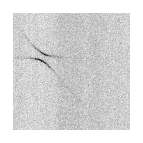

```mathematica
datapx1Z=Map[#[[3]]&,datapx1F,{2}];
{minx1,maxx1}=datapx1Z//Flatten//{Min[#],Max[#]}&
datapx1ZNorm=(datapx1Z-minx1)/(maxx1-minx1);
ArrayPlot[Transpose[datapx1ZNorm],DataReversed->True,AspectRatio->1,FrameTicks->{{{{0,rangeFreq[[1]]},{601,rangeFreq[[2]]}},None},{{{0,rangeFlux[[1]]},{121,rangeFlux[[2]]}},None}}]
```

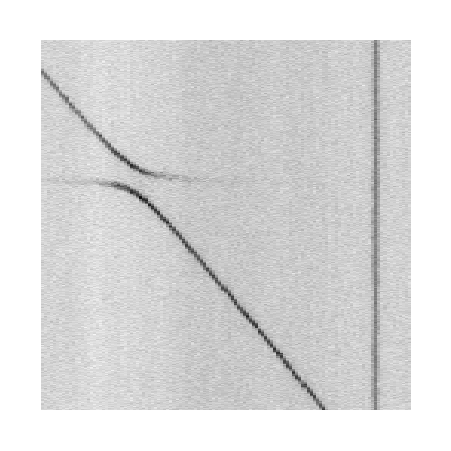

```mathematica
datap1xx1ZNorm=(datap1xZNorm+datapx1ZNorm)/2;
ArrayPlot[Transpose[datap1xx1ZNorm],DataReversed->True,AspectRatio->1,FrameTicks->{{{{0,rangeFreq[[1]]},{601,rangeFreq[[2]]}},None},{{{0,rangeFlux[[1]]},{121,rangeFlux[[2]]}},None}}]
```

```mathematica
dataToExport=Prepend[Flatten[datap1xx1F,1],{"flux","freq","p1xx1"}];
dataToExport//Dimensions
Export["U:\\Commun\\PROJET Cavités\\articles\\ISWAP\\anticrossing.dat",dataToExport,"Table"]
```

{72722,3}

U:\Commun\PROJET Cavités\articles\ISWAP\anticrossing.dat